```mathematica
filenames={"Table_TwoHerbicides_Stochastic_control2_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Stochastic_control3_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Stochastic_control4_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_Stochastic_control5_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt"};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../data/"<>filenames⟦i⟧,"CSV"],{i,1,Length[filenames],1}];
```

## Plant density/m^2

```mathematica
plottab=Table[gatherruns=GatherBy[data⟦j,2;;,{1,6,2}⟧,Last];
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotStyle->Directive[Opacity[0.05],RGBColor["#687988"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->None],PlotRange->{{0,30},{-17,6}},Axes->None],{j,1,Length[data],1}];
```

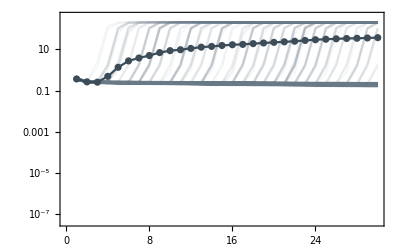
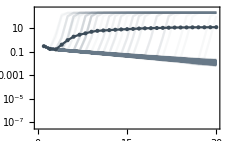
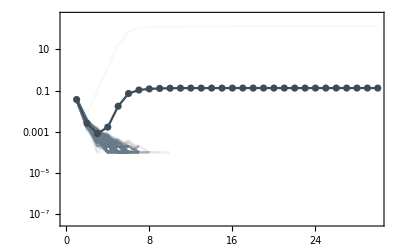
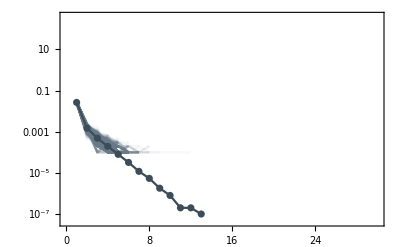

```mathematica
{{plottab⟦1⟧,plottab⟦2⟧},{plottab⟦3⟧,plottab⟦4⟧}}
```

```mathematica
plottab=Table[gatherruns=GatherBy[data⟦j,2;;,{1,6,2}⟧,Last];
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotRange->{{-0.6,30.6},{10^-7.5,10^2.7}},PlotStyle->Directive[Lighter[RGBColor["#3C4C59"],0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->None]],{j,1,Length[data],1}];
```

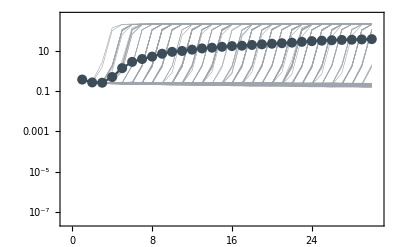
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
{{plottab⟦1⟧,plottab⟦2⟧},{plottab⟦3⟧,plottab⟦4⟧}}
```

## Pie charts

```mathematica
piedata=Table[onlydata=data⟦j⟧⟦1;;-31⟧;
onlyseason30=onlydata⟦-1000;;⟧;
sum=onlyseason30⟦All,9⟧+onlyseason30⟦All,12⟧+onlyseason30⟦All,13⟧+onlyseason30⟦All,14⟧+onlyseason30⟦All,15⟧;
(Length[sum]-Tally[sum]⟦1,2⟧)/10//N,{j,1,Length[data],1}]
```

{18.9,6.,0.1,0.}

```mathematica
Table[PieChart[{piedata⟦j⟧,100-piedata⟦j⟧},ChartStyle->{Directive[ Gray,Opacity[0.75]],White},
ChartLabels->Placed[{Style[ToString[piedata⟦j⟧]<>"% escapes",24,Black],},"RadialCallout"],ImageSize->Medium,ImagePadding->{{150,None},{-10,-10}}],{j,1,Length[data],1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}